# Quickchange Primer Design

### Script for generating optimized Quickchange primers. Below are functions needed by the program (DNA->protein translation, reverse complement, Tm score etc.)

```mathematica
translate[codon_]:=Which[codon=="GCT"||codon=="GCC"||codon=="GCA"||codon=="GCG","A",codon=="CGT"||codon=="CGC"||codon=="CGA"||codon=="CGG"||codon=="AGA"||codon=="AGG","R",codon=="AAC"||codon=="AAT","N",codon=="GAT"||codon=="GAC","D",codon=="TGT"||codon=="TGC","C",codon=="CAA"||codon=="CAG","Q",codon=="GAA"||codon=="GAG","E",codon=="GGT"||codon=="GGC"||codon=="GGA"||codon=="GGG","G",codon=="CAT"||codon=="CAC","H",codon=="ATT"||codon=="ATC"||codon=="ATA","I",codon=="TTA"||codon=="TTG"||codon=="CTT"||codon=="CTC"||codon=="CTA"||codon=="CTG","L",codon=="AAA"||codon=="AAG","K",codon=="ATG","M",codon=="TTT"||codon=="TTC","F",codon=="CCT"||codon=="CCC"||codon=="CCA"||codon=="CCG","P",codon=="TCT"||codon=="TCC"||codon=="TCA"||codon=="TCG"||codon=="AGT"||codon=="AGC","S",codon=="ACT"||codon=="ACC"||codon=="ACA"||codon=="ACG","T",codon=="TGG","W",codon=="TAT"||codon=="TAC","Y",codon=="GTT"||codon=="GTC"||codon=="GTA"||codon=="GTG","V"]

getcomplement[base_]:=Which[base=="G","C",base=="C","G",base=="T","A",base=="A","T"]

reversecomplement[sequence_]:=Module[{temp1,complement},

temp1=Characters[sequence];

complement=Table[getcomplement[temp1[[i]]],{i,1,Length[temp1]}];

StringJoin[Reverse[complement]]

]

primerparams[sequence_,annealingportion_,mismatch_]:=Module[{n,g,c,gc},

n=StringLength[sequence];

g=StringCount[sequence,"G"];

c=StringCount[sequence,"C"];

gc=(g+c)/n*100.0;

(*Print[TableForm[{{"Length","%GC","Tm"},{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}}]];*)

{n,gc,81.5+0.41*gc-(675.0/n)-mismatch/42*100.}

]

Tmscore[Tm_]:=Piecewise[{{2,Tm≥78.0&&Tm<82.0},{(Tm-77.0)+1,Tm<78.0},{-1*(Tm-82.0)+2,Tm≥82.0}}]

alanine={"GCT","GCC","GCA","GCG"};

arginine={"CGT","CGC","CGA","CGG","AGA","AGG"};

asparagine={"AAC","AAT"};

aspartate={"GAT","GAC"};

cysteine={"TGT","TGC"};

glutamine={"CAA","CAG"};

glutamate={"GAA","GAG"};

glycine={"GGT","GGC","GGA","GGG"};

histidine={"CAT","CAC"};

isoleucine={"ATT","ATC","ATA"};

leucine={"TTA","TTG","CTT","CTC","CTA","CTG"};

lysine={"AAA","AAG"};

methionine={"ATG"};

phenylalanine={"TTT","TTC"};

proline={"CCT","CCC","CCA","CCG"};

serine={"TCT","TCC","TCA","TCG","AGT","AGC"};

threonine={"ACT","ACC","ACA","ACG"};

tryptophan={"TGG"};

tyrosine={"TAT","TAC"};

valine={"GTT","GTC","GTA","GTG"};
```

### Open an external Python process to calculate hairpin Tms using Primer3:

```mathematica
Tmcounter=0;

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

calcHairpin[sequence_]:=(

Tmcounternew=Tmcounter+1;

path="/usr/local/bin/python2.7";

If[Tmcounternew==500,

(KillProcess[pythonpath];

pythonpath=StartProcess[{path,"-i"}];

cmd="import primer3";
Pause[0.001];
WriteLine[pythonpath,cmd];

Tmcounternew=0)];

cmd=StringJoin["primer3.calcHairpin('",sequence,"').tm"];
Pause[0.001];

WriteLine[pythonpath,cmd];

Pause[0.05];

out=ReadString[pythonpath,EndOfBuffer];

Tmcounter=Tmcounternew;

out)
```

### Test if the Tm calculation works (you may need to evaluate the cell above 2x):

```mathematica
calcHairpin["GCACATTCTGTGGGCTTTGGGCAAGCACATAAAATGCC"]
```

58.19360163176441

### Read in DNA sequence of interest, and translate:

```mathematica
pafAsequence="ATGGGCCGTACAACTTCTGAGGGAATACACGGTTTTGTGGACGATCTAGAGCCCAAGAGCAGCATTCTTGATAAAGTCGGAGACTTTATCACCGTAAACACGAAACGGCATGATGGGCGCGAGGACTTCAACGAGCAAAACGACGAGCTGAACAGTCAAGAGAACCACAACAGCAGTGAGAATGGGAACGAGAATGAAAATGAACAAGACAGTCTCGCGTTGGACGACCTAGACCGCGCCTTTGAGCTGGTGGAAGGTATGGATATGGACTGGATGATGCCCTCGCATGCGCACCACTCCCCAGCTACAACTGCTACAATCAAGCCGCGGCTATTATATTCGCCGCTAATACACACGCAAAGTGCGGTTCCCGTAACCATTTCGCCGAACTTGGTCGCTACTGCTACTTCCACCACATCCGCTAACAAAGTCACTAAAAACAAGAGTAATAGTAGTCCGTATTTGAACAAGCGCAGAGGTAAACCCGGGCCGGATTCGGCCACTTCGCTGTTCGAATTGCCCGACAGCGTTATCCCAACTCCGAAACCGAAACCGAAACCAAAGCAATATCCGAAAGTTATTCTGCCGTCGAACAGCACAAGACGCGTATCACCGGTCACGGCCAAGACCAGCAGCAGCGCAGAAGGCGTGGTCGTAGCAAGTGAGTCTCCTGTAATCGCGCCGCACGGATCGAGCCATTCGCGGTCGCTGAGTAAGCGACGGTCATCGGGCGCGCTCGTGGACGATGACAAGCGCGAATCACACAAGCATGCAGAGCAAGCACGGCGTAATCGATTAGCGGTCGCGCTGCACGAACTGGCGTCTTTAATCCCCGCGGAGTGGAAACAGCAAAATGTGTCGGCCGCGCCGTCCAAAGCGACCACCGTGGAGGCGGCCTGCCGGTACATCCGTCACCTACAGCAGAACGTGAGCACGGGAGGAGGGTCTGGGGGAGGAGGCAGTGGCATGGTGAGCAAGGGCGAGGAGCTGTTCACCGGGGTGGTGCCCATCCTGGTCGAGCTGGACGGC";

pafAcodons=Partition[Characters[pafAsequence],3];
```

```mathematica
(* translate *)

translation=Table[{i,StringJoin["Res ",ToString[i*3-2]],StringJoin[pafAcodons[[i]]],Style[translate[StringJoin[pafAcodons[[i]]]],Bold]},{i,1,Length[pafAcodons]}]
```

{{1,Res 1,ATG,M},{2,Res 4,GGC,G},{3,Res 7,CGT,R},{4,Res 10,ACA,T},{5,Res 13,ACT,T},{6,Res 16,TCT,S},{7,Res 19,GAG,E},{8,Res 22,GGA,G},{9,Res 25,ATA,I},{10,Res 28,CAC,H},{11,Res 31,GGT,G},{12,Res 34,TTT,F},{13,Res 37,GTG,V},{14,Res 40,GAC,D},{15,Res 43,GAT,D},{16,Res 46,CTA,L},{17,Res 49,GAG,E},{18,Res 52,CCC,P},{19,Res 55,AAG,K},{20,Res 58,AGC,S},{21,Res 61,AGC,S},{22,Res 64,ATT,I},{23,Res 67,CTT,L},{24,Res 70,GAT,D},{25,Res 73,AAA,K},{26,Res 76,GTC,V},{27,Res 79,GGA,G},{28,Res 82,GAC,D},{29,Res 85,TTT,F},{30,Res 88,ATC,I},{31,Res 91,ACC,T},{32,Res 94,GTA,V},{33,Res 97,AAC,N},{34,Res 100,ACG,T},{35,Res 103,AAA,K},{36,Res 106,CGG,R},{37,Res 109,CAT,H},{38,Res 112,GAT,D},{39,Res 115,GGG,G},{40,Res 118,CGC,R},{41,Res 121,GAG,E},{42,Res 124,GAC,D},{43,Res 127,TTC,F},{44,Res 130,AAC,N},{45,Res 133,GAG,E},{46,Res 136,CAA,Q},{47,Res 139,AAC,N},{48,Res 142,GAC,D},{49,Res 145,GAG,E},{50,Res 148,CTG,L},{51,Res 151,AAC,N},{52,Res 154,AGT,S},{53,Res 157,CAA,Q},{54,Res 160,GAG,E},{55,Res 163,AAC,N},{56,Res 166,CAC,H},{57,Res 169,AAC,N},{58,Res 172,AGC,S},{59,Res 175,AGT,S},{60,Res 178,GAG,E},{61,Res 181,AAT,N},{62,Res 184,GGG,G},{63,Res 187,AAC,N},{64,Res 190,GAG,E},{65,Res 193,AAT,N},{66,Res 196,GAA,E},{67,Res 199,AAT,N},{68,Res 202,GAA,E},{69,Res 205,CAA,Q},{70,Res 208,GAC,D},{71,Res 211,AGT,S},{72,Res 214,CTC,L},{73,Res 217,GCG,A},{74,Res 220,TTG,L},{75,Res 223,GAC,D},{76,Res 226,GAC,D},{77,Res 229,CTA,L},{78,Res 232,GAC,D},{79,Res 235,CGC,R},{80,Res 238,GCC,A},{81,Res 241,TTT,F},{82,Res 244,GAG,E},{83,Res 247,CTG,L},{84,Res 250,GTG,V},{85,Res 253,GAA,E},{86,Res 256,GGT,G},{87,Res 259,ATG,M},{88,Res 262,GAT,D},{89,Res 265,ATG,M},{90,Res 268,GAC,D},{91,Res 271,TGG,W},{92,Res 274,ATG,M},{93,Res 277,ATG,M},{94,Res 280,CCC,P},{95,Res 283,TCG,S},{96,Res 286,CAT,H},{97,Res 289,GCG,A},{98,Res 292,CAC,H},{99,Res 295,CAC,H},{100,Res 298,TCC,S},{101,Res 301,CCA,P},{102,Res 304,GCT,A},{103,Res 307,ACA,T},{104,Res 310,ACT,T},{105,Res 313,GCT,A},{106,Res 316,ACA,T},{107,Res 319,ATC,I},{108,Res 322,AAG,K},{109,Res 325,CCG,P},{110,Res 328,CGG,R},{111,Res 331,CTA,L},{112,Res 334,TTA,L},{113,Res 337,TAT,Y},{114,Res 340,TCG,S},{115,Res 343,CCG,P},{116,Res 346,CTA,L},{117,Res 349,ATA,I},{118,Res 352,CAC,H},{119,Res 355,ACG,T},{120,Res 358,CAA,Q},{121,Res 361,AGT,S},{122,Res 364,GCG,A},{123,Res 367,GTT,V},{124,Res 370,CCC,P},{125,Res 373,GTA,V},{126,Res 376,ACC,T},{127,Res 379,ATT,I},{128,Res 382,TCG,S},{129,Res 385,CCG,P},{130,Res 388,AAC,N},{131,Res 391,TTG,L},{132,Res 394,GTC,V},{133,Res 397,GCT,A},{134,Res 400,ACT,T},{135,Res 403,GCT,A},{136,Res 406,ACT,T},{137,Res 409,TCC,S},{138,Res 412,ACC,T},{139,Res 415,ACA,T},{140,Res 418,TCC,S},{141,Res 421,GCT,A},{142,Res 424,AAC,N},{143,Res 427,AAA,K},{144,Res 430,GTC,V},{145,Res 433,ACT,T},{146,Res 436,AAA,K},{147,Res 439,AAC,N},{148,Res 442,AAG,K},{149,Res 445,AGT,S},{150,Res 448,AAT,N},{151,Res 451,AGT,S},{152,Res 454,AGT,S},{153,Res 457,CCG,P},{154,Res 460,TAT,Y},{155,Res 463,TTG,L},{156,Res 466,AAC,N},{157,Res 469,AAG,K},{158,Res 472,CGC,R},{159,Res 475,AGA,R},{160,Res 478,GGT,G},{161,Res 481,AAA,K},{162,Res 484,CCC,P},{163,Res 487,GGG,G},{164,Res 490,CCG,P},{165,Res 493,GAT,D},{166,Res 496,TCG,S},{167,Res 499,GCC,A},{168,Res 502,ACT,T},{169,Res 505,TCG,S},{170,Res 508,CTG,L},{171,Res 511,TTC,F},{172,Res 514,GAA,E},{173,Res 517,TTG,L},{174,Res 520,CCC,P},{175,Res 523,GAC,D},{176,Res 526,AGC,S},{177,Res 529,GTT,V},{178,Res 532,ATC,I},{179,Res 535,CCA,P},{180,Res 538,ACT,T},{181,Res 541,CCG,P},{182,Res 544,AAA,K},{183,Res 547,CCG,P},{184,Res 550,AAA,K},{185,Res 553,CCG,P},{186,Res 556,AAA,K},{187,Res 559,CCA,P},{188,Res 562,AAG,K},{189,Res 565,CAA,Q},{190,Res 568,TAT,Y},{191,Res 571,CCG,P},{192,Res 574,AAA,K},{193,Res 577,GTT,V},{194,Res 580,ATT,I},{195,Res 583,CTG,L},{196,Res 586,CCG,P},{197,Res 589,TCG,S},{198,Res 592,AAC,N},{199,Res 595,AGC,S},{200,Res 598,ACA,T},{201,Res 601,AGA,R},{202,Res 604,CGC,R},{203,Res 607,GTA,V},{204,Res 610,TCA,S},{205,Res 613,CCG,P},{206,Res 616,GTC,V},{207,Res 619,ACG,T},{208,Res 622,GCC,A},{209,Res 625,AAG,K},{210,Res 628,ACC,T},{211,Res 631,AGC,S},{212,Res 634,AGC,S},{213,Res 637,AGC,S},{214,Res 640,GCA,A},{215,Res 643,GAA,E},{216,Res 646,GGC,G},{217,Res 649,GTG,V},{218,Res 652,GTC,V},{219,Res 655,GTA,V},{220,Res 658,GCA,A},{221,Res 661,AGT,S},{222,Res 664,GAG,E},{223,Res 667,TCT,S},{224,Res 670,CCT,P},{225,Res 673,GTA,V},{226,Res 676,ATC,I},{227,Res 679,GCG,A},{228,Res 682,CCG,P},{229,Res 685,CAC,H},{230,Res 688,GGA,G},{231,Res 691,TCG,S},{232,Res 694,AGC,S},{233,Res 697,CAT,H},{234,Res 700,TCG,S},{235,Res 703,CGG,R},{236,Res 706,TCG,S},{237,Res 709,CTG,L},{238,Res 712,AGT,S},{239,Res 715,AAG,K},{240,Res 718,CGA,R},{241,Res 721,CGG,R},{242,Res 724,TCA,S},{243,Res 727,TCG,S},{244,Res 730,GGC,G},{245,Res 733,GCG,A},{246,Res 736,CTC,L},{247,Res 739,GTG,V},{248,Res 742,GAC,D},{249,Res 745,GAT,D},{250,Res 748,GAC,D},{251,Res 751,AAG,K},{252,Res 754,CGC,R},{253,Res 757,GAA,E},{254,Res 760,TCA,S},{255,Res 763,CAC,H},{256,Res 766,AAG,K},{257,Res 769,CAT,H},{258,Res 772,GCA,A},{259,Res 775,GAG,E},{260,Res 778,CAA,Q},{261,Res 781,GCA,A},{262,Res 784,CGG,R},{263,Res 787,CGT,R},{264,Res 790,AAT,N},{265,Res 793,CGA,R},{266,Res 796,TTA,L},{267,Res 799,GCG,A},{268,Res 802,GTC,V},{269,Res 805,GCG,A},{270,Res 808,CTG,L},{271,Res 811,CAC,H},{272,Res 814,GAA,E},{273,Res 817,CTG,L},{274,Res 820,GCG,A},{275,Res 823,TCT,S},{276,Res 826,TTA,L},{277,Res 829,ATC,I},{278,Res 832,CCC,P},{279,Res 835,GCG,A},{280,Res 838,GAG,E},{281,Res 841,TGG,W},{282,Res 844,AAA,K},{283,Res 847,CAG,Q},{284,Res 850,CAA,Q},{285,Res 853,AAT,N},{286,Res 856,GTG,V},{287,Res 859,TCG,S},{288,Res 862,GCC,A},{289,Res 865,GCG,A},{290,Res 868,CCG,P},{291,Res 871,TCC,S},{292,Res 874,AAA,K},{293,Res 877,GCG,A},{294,Res 880,ACC,T},{295,Res 883,ACC,T},{296,Res 886,GTG,V},{297,Res 889,GAG,E},{298,Res 892,GCG,A},{299,Res 895,GCC,A},{300,Res 898,TGC,C},{301,Res 901,CGG,R},{302,Res 904,TAC,Y},{303,Res 907,ATC,I},{304,Res 910,CGT,R},{305,Res 913,CAC,H},{306,Res 916,CTA,L},{307,Res 919,CAG,Q},{308,Res 922,CAG,Q},{309,Res 925,AAC,N},{310,Res 928,GTG,V},{311,Res 931,AGC,S},{312,Res 934,ACG,T},{313,Res 937,GGA,G},{314,Res 940,GGA,G},{315,Res 943,GGG,G},{316,Res 946,TCT,S},{317,Res 949,GGG,G},{318,Res 952,GGA,G},{319,Res 955,GGA,G},{320,Res 958,GGC,G},{321,Res 961,AGT,S},{322,Res 964,GGC,G},{323,Res 967,ATG,M},{324,Res 970,GTG,V},{325,Res 973,AGC,S},{326,Res 976,AAG,K},{327,Res 979,GGC,G},{328,Res 982,GAG,E},{329,Res 985,GAG,E},{330,Res 988,CTG,L},{331,Res 991,TTC,F},{332,Res 994,ACC,T},{333,Res 997,GGG,G},{334,Res 1000,GTG,V},{335,Res 1003,GTG,V},{336,Res 1006,CCC,P},{337,Res 1009,ATC,I},{338,Res 1012,CTG,L},{339,Res 1015,GTC,V},{340,Res 1018,GAG,E},{341,Res 1021,CTG,L},{342,Res 1024,GAC,D},{343,Res 1027,GGC,G}}

### Provide list of subset of mutants with bad hairpin Tms from other notebook:

```mathematica
mutation={"S230A","S231A","H233A","R235A","L237A","S238A","R240A","S242A","S231V","H233V","L237V","S238V","K239V","R241V"};
```

### Below generates the optimized Quickchange primers, with additional optimization for hairpin Tm:

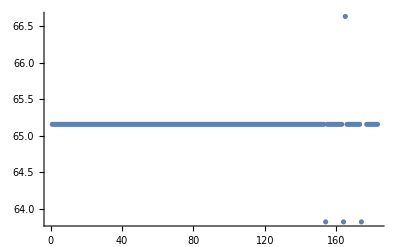

{S230A,{{GTAATCGCGCCGCACGCATCGAGCCATTC,{29,62.069,81.2915},-1.14657,65.1552},{GTAATCGCGCCGCACGCATCGAGCCATTCG,{30,63.3333,82.5857},-1.98228,65.1552},{TGTAATCGCGCCGCACGCATCGAGCCATTC,{30,60.,81.219},-2.14657,65.1552}}}

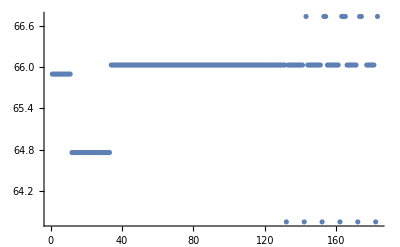

{S231A,{{CGCGCCGCACGGAGCGAGCCATTC,{24,75.,81.744},-1.02773,64.7591},{GCGCCGCACGGAGCGAGCCATTC,{23,73.913,80.0756},-1.36939,65.898},{GCGCCGCACGGAGCGAGCCATTCG,{24,75.,81.744},-1.61939,65.898}}}

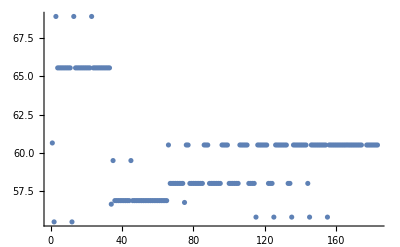

{H233A,{{GCACGGATCGAGCGCTTCGCGGTC,{24,70.8333,77.6548},1.4165,55.4609},{CACGGATCGAGCGCTTCGCGGTC,{23,69.5652,75.912},-0.326251,55.4609},{CCGCACGGATCGAGCGCTTCGCGGTCGC,{28,75.,83.381},-0.967823,56.6229}}}

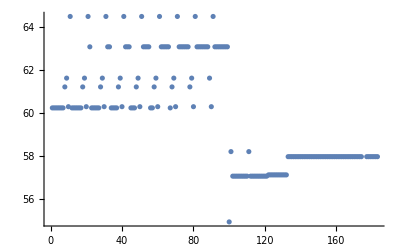

{R235A,{{CGGATCGAGCCATTCGGCGTCGCTGAGTAAG,{31,61.2903,80.0929},0.325879,60.2471},{GATCGAGCCATTCGGCGTCGCTGAGTAAGCGAC,{33,60.6061,81.132},0.30897,60.3034},{CGGATCGAGCCATTCGGCGTCGCTGAGTAAGC,{32,62.5,81.2693},0.0758789,60.2471}}}

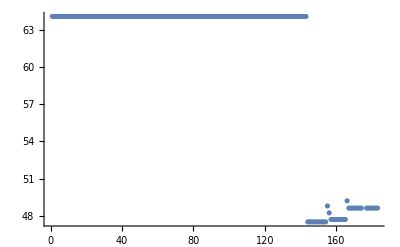

{L237A,{{GCCATTCGCGGTCGGCGAGTAAGCGAC,{27,66.6667,79.0714},-0.818799,64.0627},{CATTCGCGGTCGGCGAGTAAGCGACGGTCATC,{32,62.5,81.2693},-0.818799,64.0627},{CATTCGCGGTCGGCGAGTAAGCGACGGTC,{29,65.5172,80.3243},-0.818799,64.0627}}}

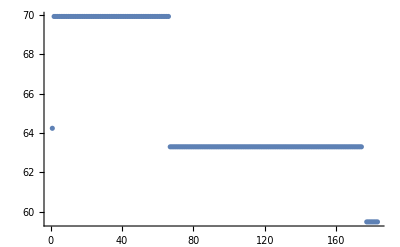

{S238A,{{CATTCGCGGTCGCTGGCTAAGCGACGGTCATC,{32,62.5,81.2693},-2.57985,69.9328},{CATTCGCGGTCGCTGGCTAAGCGACGGTC,{29,65.5172,80.3243},-2.57985,69.9328},{GAGCCATTCGCGGTCGCTGGCTAAGCGACGGTCATC,{36,63.8889,84.1825},-2.77115,63.2954}}}

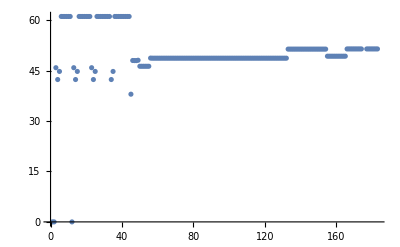

{R240A,{{GCGGTCGCTGAGTAAGGCACGGTCATCGGG,{30,66.6667,81.5714},3.75,37.9957},{CGGTCGCTGAGTAAGGCACGGTCATCGGG,{29,65.5172,80.3243},3.75,44.7662},{CGGTCGCTGAGTAAGGCACGGTCATCGG,{28,64.2857,78.9881},3.75,42.3578}}}

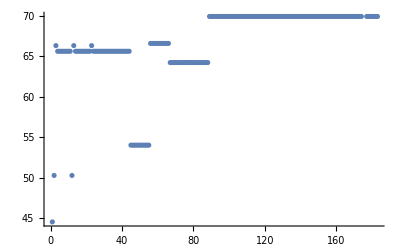

{S242A,{{GAGTAAGCGACGGGCATCGGGCGC,{24,70.8333,80.0357},3.06339,50.2887},{AGTAAGCGACGGGCATCGGGCGC,{23,69.5652,78.293},2.06339,50.2887},{AGTAAGCGACGGGCATCGGGCG,{22,68.1818,76.3918},0.641775,44.5502}}}

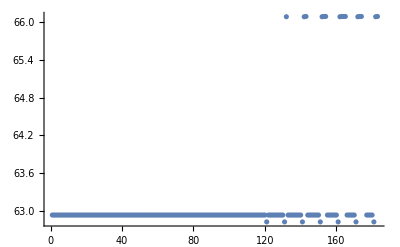

{S231V,{{CGCGCCGCACGGAGTGAGCCATTCGC,{26,73.0769,80.7381},-0.729425,62.9314},{GCGCCGCACGGAGTGAGCCATTCGCG,{26,73.0769,80.7381},-0.729425,62.9314},{CGCGCCGCACGGAGTGAGCCATTC,{24,70.8333,77.6548},-0.824663,62.9314}}}

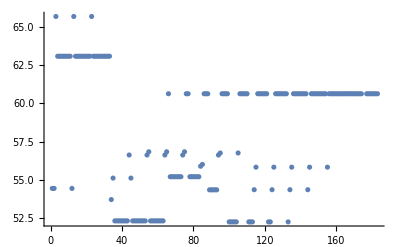

{H233V,{{CCGCACGGATCGAGCGTTTCGCGGTCGCTG,{30,70.,82.9381},1.51101,52.3363},{CCGCACGGATCGAGCGTTTCGCGGTCGC,{28,71.4286,81.9167},1.28193,53.7269},{CCGCACGGATCGAGCGTTTCGCGGTCGCTGA,{31,67.7419,82.7381},0.71101,52.3363}}}

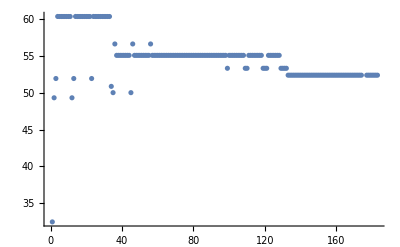

{L237V,{{GAGCCATTCGCGGTCGGTGAGTAAGCGACG,{30,63.3333,82.5857},2.56532,49.9966},{AGCCATTCGCGGTCGGTGAGTAAGCGAC,{28,60.7143,79.9048},2.14544,50.8485},{GCCATTCGCGGTCGGTGAGTAAGCGA,{26,61.5385,78.3883},1.82619,51.9127}}}

-Graphics-

{S238V,{{GAGCCATTCGCGGTCGCTGGTTAAGCGACGGTCATC,{36,61.1111,83.0437},-1.63226,63.2954},{AGCCATTCGCGGTCGCTGGTTAAGCGACGGTCATC,{35,60.,82.0524},-1.64099,63.2954},{CATTCGCGGTCGCTGGTTAAGCGACGGTCATC,{32,59.375,79.9881},-2.57985,69.9328}}}

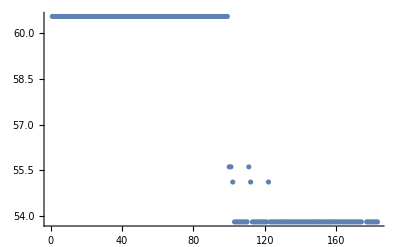

{K239V,{{CGCGGTCGCTGAGTGTGCGACGGTCATC,{28,67.8571,80.4524},0.238075,60.5397},{GCGGTCGCTGAGTGTGCGACGGTCATC,{27,66.6667,79.0714},0.238075,60.5397},{GCGGTCGCTGAGTGTGCGACGGTCATCGG,{29,68.9655,81.7381},-0.0119245,60.5397}}}

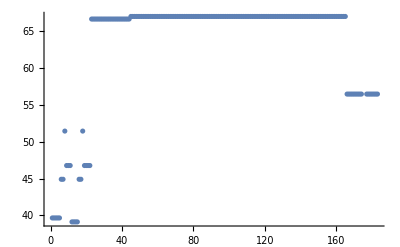

{R241V,{{GCTGAGTAAGCGAGTGTCATCGGGCGCGCTC,{31,64.5161,81.4155},4.,46.7632},{CTGAGTAAGCGAGTGTCATCGGGCGCGCTC,{30,63.3333,80.2048},4.,46.7632},{GCTGAGTAAGCGAGTGTCATCGGGCGCG,{28,64.2857,78.9881},3.75,44.9028}}}

```mathematica
Dynamic[loop]
Dynamic[i]

Do[

resnumber=ToExpression[StringDrop[StringDrop[mutation[[loop]],{1}],{-1}]];

restypeIN=StringTake[mutation[[loop]],{-1}];

(* calculate the number of base pair changes between the wild-type sequence and all codons of the mutated amino acid *)
newrescodons=Which[restypeIN=="A",alanine,restypeIN=="G",glycine,restypeIN=="D",aspartate,restypeIN=="N",asparagine,restypeIN=="E",glutamate,restypeIN=="Q",glutamine,restypeIN=="V",valine,restypeIN=="L",leucine,restypeIN=="I",isoleucine,restypeIN=="P",proline,restypeIN=="H",histidine,restypeIN=="K",lysine,restypeIN=="R",arginine,restypeIN=="Y",tyrosine,restypeIN=="F",phenylalanine,restypeIN=="W",tryptophan,restypeIN=="S",serine,restypeIN=="T",threonine,restypeIN=="C",cysteine,restypeIN=="M",methionine];

testwt=pafAcodons[[resnumber]];
(*Print[testwt];

Print[translation[[resnumber]]];*)

Do[

testmutant=Characters[newrescodons[[i]]];

codondiff[i]=If[testwt[[1]]==testmutant[[1]],0,1]+If[testwt[[2]]==testmutant[[2]],0,1]+If[testwt[[3]]==testmutant[[3]],0,1];

,{i,1,Length[newrescodons]}];

(* select codon requiring the least number of base pair changes *)
newcodon=Sort[Table[{StringJoin[newrescodons[[i]]],codondiff[i]},{i,1,Length[newrescodons]}],#1[[2]]<#2[[2]]&][[1]];

(*Print["New codon"];
Print[newcodon];*)

(* test a range of flanking lengths *)
base5prime=resnumber*3-2;
base3prime=resnumber*3;

(* below plots the piecewise function used by Tmscore *)
(* Plot[Piecewise[{{2,Tm≥78.0},{(Tm-77.0)+1,Tm≥77.0},{(Tm-70.0)*0.142857,Tm<77.0}}],{Tm,70,85}] *)

(* counter for indexing the mutagenic primers *)
counter=0;

Do[

Do[

fiveprimeend=base5prime-i;
threeprimeend=base3prime+j;

wildtypeprimer=StringTake[pafAsequence,{fiveprimeend,threeprimeend}];

(* insert mutation into sense primer *)
mutagenicprimer=StringJoin[StringTake[pafAsequence,{fiveprimeend,base5prime-1}],StringJoin[newcodon[[1]]],StringTake[pafAsequence,{base3prime+1,threeprimeend}]];

gcfirst=If[StringTake[mutagenicprimer,1]=="G"||StringTake[mutagenicprimer,1]=="C",1,0];

gclast=If[StringTake[mutagenicprimer,-1]=="G"||StringTake[mutagenicprimer,-1]=="C",1,0];

(* calculate the annealing portion of the sequence for Tm calcuations *)
wtseq=Characters[wildtypeprimer];
mutantseq=Characters[mutagenicprimer];

seqforTm=StringJoin[Select[Table[If[wtseq[[i]]==mutantseq[[i]],wtseq[[i]]],{i,1,Length[wtseq]}],#=="G"||#=="C"||#=="A"||#=="T"&]];

(* use "primerparams" function to calculate %GC and melting temperature *)
parameters=primerparams[mutagenicprimer,seqforTm,newcodon[[2]]];

(* include penalties for primer 3' self-complementarity *)
onebase=If[getcomplement[StringTake[mutagenicprimer,-1]]==StringTake[mutagenicprimer,{-2}],-0.25,0];
twobases=If[getcomplement[StringTake[mutagenicprimer,{2}]]==StringTake[mutagenicprimer,{-2}]&&onebase==-0.25,-0.5,0];
threebases=If[getcomplement[StringTake[mutagenicprimer,{3}]]==StringTake[mutagenicprimer,{-3}]&&twobases==-0.25,-1.0,0];

(* hairpin penalty function *)
hairpin=Piecewise[{{0,hTm<48.0},{-0.3*hTm+0.3*48.0,hTm≥48.0}}];

hairpinTm=ToExpression[calcHairpin[mutagenicprimer]];

(* calculate final "objective function" score *)
(* 06/24/26 - included a penalty for longer primers (to reduce oligo synthesis costs) *)
endscore=gcfirst+gclast+Tmscore[parameters[[3]]]+If[StringLength[mutagenicprimer]>19*2&&parameters[[3]]>79.0,(-0.04*StringLength[mutagenicprimer]),0]+If[StringTake[mutagenicprimer,{-1}]==StringTake[mutagenicprimer,{-2}],-0.25,0.0]+If[StringTake[mutagenicprimer,{1}]==StringTake[mutagenicprimer,{2}],-0.25,0.0]+onebase+twobases+threebases+(hairpin/.{hTm->hairpinTm});

(* need to clear the self-complementarity tests otherwise will be included in calculations for subsequent primers *)
Clear[onebase,twobases,threebases];

(* counter *)
counter2=counter+1;
counter=counter2;

primertest[counter]={mutagenicprimer,parameters,endscore,hairpinTm};

,{j,i-5,i+5}]

,{i,12,28}];

allprimers=Table[primertest[m],{m,1,counter}];

(*Print[allprimers];*)

Print[ListPlot[allprimers[[All,4]],PlotRange->All]];

best[mutation[[loop]]]={mutation[[loop]],Select[Sort[allprimers,#1[[3]]>#2[[3]]&],#[[2,1]]<50&][[1;;3]]};

Print[best[mutation[[loop]]]];

,{loop,1,Length[mutation]}]
```

### Write out list of top “hit” for each mutant, and calculate hairpin Tm for all:

```mathematica
mutationproperresnums=Table[StringJoin[StringTake[mutation[[n]],1],ToString[ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]]],StringTake[mutation[[n]],-1]],{n,1,Length[mutation]}];

Dynamic[n]

primers=Table[{ToExpression[StringDrop[StringDrop[mutation[[n]],-1],1]],mutationproperresnums[[n]],best[mutation[[n]]][[2,1,1]],"","","","","",reversecomplement[best[mutation[[n]]][[2,1,1]]],ToExpression[calcHairpin[best[mutation[[n]]][[2,1,1]]]]},{n,1,Length[mutation]}]
```

{{230,S230A,GTAATCGCGCCGCACGCATCGAGCCATTC,,,,,,GAATGGCTCGATGCGTGCGGCGCGATTAC,65.1552},{231,S231A,CGCGCCGCACGGAGCGAGCCATTC,,,,,,GAATGGCTCGCTCCGTGCGGCGCG,64.7591},{233,H233A,GCACGGATCGAGCGCTTCGCGGTC,,,,,,GACCGCGAAGCGCTCGATCCGTGC,55.4609},{235,R235A,CGGATCGAGCCATTCGGCGTCGCTGAGTAAG,,,,,,CTTACTCAGCGACGCCGAATGGCTCGATCCG,60.2471},{237,L237A,GCCATTCGCGGTCGGCGAGTAAGCGAC,,,,,,GTCGCTTACTCGCCGACCGCGAATGGC,64.0627},{238,S238A,CATTCGCGGTCGCTGGCTAAGCGACGGTCATC,,,,,,GATGACCGTCGCTTAGCCAGCGACCGCGAATG,69.9328},{240,R240A,GCGGTCGCTGAGTAAGGCACGGTCATCGGG,,,,,,CCCGATGACCGTGCCTTACTCAGCGACCGC,37.9957},{242,S242A,GAGTAAGCGACGGGCATCGGGCGC,,,,,,GCGCCCGATGCCCGTCGCTTACTC,50.2887},{231,S231V,CGCGCCGCACGGAGTGAGCCATTCGC,,,,,,GCGAATGGCTCACTCCGTGCGGCGCG,62.9314},{233,H233V,CCGCACGGATCGAGCGTTTCGCGGTCGCTG,,,,,,CAGCGACCGCGAAACGCTCGATCCGTGCGG,52.3363},{237,L237V,GAGCCATTCGCGGTCGGTGAGTAAGCGACG,,,,,,CGTCGCTTACTCACCGACCGCGAATGGCTC,49.9966},{238,S238V,GAGCCATTCGCGGTCGCTGGTTAAGCGACGGTCATC,,,,,,GATGACCGTCGCTTAACCAGCGACCGCGAATGGCTC,63.2954},{239,K239V,CGCGGTCGCTGAGTGTGCGACGGTCATC,,,,,,GATGACCGTCGCACACTCAGCGACCGCG,60.5397},{241,R241V,GCTGAGTAAGCGAGTGTCATCGGGCGCGCTC,,,,,,GAGCGCGCCCGATGACACTCGCTTACTCAGC,46.7632}}

### Select primers that have hairpin Tm > 50C:

```mathematica
Export["/Users/craig/Dropbox/craig_analysis_and_simulation_code/Arjun_mutagenesis/PHO4_mutagenesis/180611_PHO4_N-termScan_Primers_WITHHairpinOptimization.csv", primers]
```

/Users/craig/Dropbox/craig_analysis_and_simulation_code/Arjun_mutagenesis/PHO4_mutagenesis/180611_PHO4_N-termScan_Primers_WITHHairpinOptimization.csv